```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
datac=Import["vtracer.output.csv"];
Dimensions@datac
```

{28,30028}

```mathematica
upc=Pick[datac⟦1,2;;-1⟧,Table[Max@DeleteCases[datac⟦3;;-1,i⟧,""]>490000,{i,2,30028}]];
Dimensions@upc
```

{240}

```mathematica
datac⟦3;;-1,1⟧=Table[DateString[FromUnixTime@(datac⟦j,1⟧/1000),{"Year","Month","Day","Hour"}],{j,3,28}]
```

{2018091611,2018091623,2018091711,2018091723,2018091811,2018091823,2018091911,2018091923,2018092011,2018092023,2018092111,2018092123,2018092211,2018092223,2018092311,2018092323,2018092411,2018092423,2018092511,2018092523,2018092611,2018092623,2018092711,2018092723,2018092811,2018092823}

## 合并数据

```mathematica
dataa=Import["rs10w+用于掠过特别篇//data.csv"];
Dimensions@dataa
```

{62,1509}

```mathematica
dataa⟦1,All⟧
```

```mathematica
expo=Table[
Join[
Select[Table[dataa⟦All,j⟧,{j,2,1509}],#⟦1⟧==upc⟦j⟧&]⟦1⟧,
Select[Table[IntegerPart@datac⟦All,j⟧,{j,2,30028}],#⟦1⟧==upc⟦j⟧&]⟦1⟧
],
{j,1,Length@upc}];
```

Part::partw: {} 的部分 1 不存在.

Join::heads: 位置 1 和 2 处的头部 Part 和 List 应该是一样的.

```mathematica
Export["49w+.csv",Prepend[expo,
Join[dataa⟦All,1⟧,datac⟦All,1⟧]
],CharacterEncoding->"CP936"]
```

49w+.csv

## 还是得插值补洞……

```mathematica
data=Import["49w+.csv"];
```

```mathematica
Dimensions@data
```

{59,240}

```mathematica
time=data⟦4;;-1,1⟧;
```

```mathematica
todate[i_]:=DateObject@ToExpression@{StringTake[ToString@time⟦i⟧,4],StringTake[ToString@time⟦i⟧,{5,6}],StringTake[ToString@time⟦i⟧,{7,8}],StringTake[ToString@time⟦i⟧,{9,10}]}
```

```mathematica
timeO=Table[todate[i],{i,Length@time}];
```

```mathematica
ts[i_]:=(
p=Pick[Table[{timeO⟦j⟧,data⟦j+3,i⟧},{j,Length@timeO}],
Table[data⟦j+3,i⟧≠""&&data⟦j+3,i⟧>70000,{j,Length@timeO}]];
TimeSeries[p⟦All,2⟧,{p⟦All,1⟧},ResamplingMethod->{"Interpolation",InterpolationOrder->2}]
)
```

```mathematica
rs[i_]:=TimeSeriesResample[ts[i],{DateObject[{2018,9,1,11}],Automatic,0.5},ResamplingMethod->{"Interpolation",InterpolationOrder->1}]
```

InterpolatingFunction::dmval: 输入值 {3744788400} 位于插值函数的数据范围之外. 将使用外推法.

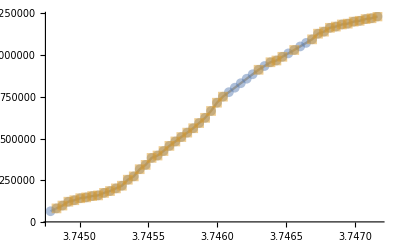

```mathematica
ListLinePlot[{rs[232],ts[232]},PlotStyle->Opacity[.5],PlotMarkers->{Automatic, 10},Mesh->All]
```

```mathematica
rs[i_]:=TimeSeriesResample[ts[i],{DateObject[{2018,9,1,11}],Automatic,0.5},ResamplingMethod->{"Interpolation",InterpolationOrder->2}]
```

InterpolatingFunction::dmval: 输入值 {3744788400} 位于插值函数的数据范围之外. 将使用外推法.

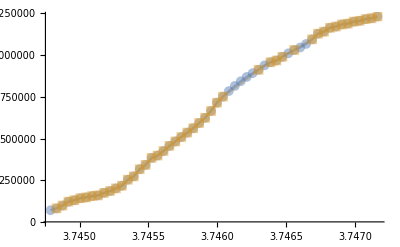

```mathematica
ListLinePlot[{rs[232],ts[232]},PlotStyle->Opacity[.5],PlotMarkers->{Automatic, 10},Mesh->All]
```

```mathematica
Export["rs-49w+.csv",Join[DateString/@DateObject/@rs[2]["Times"],
Table[Prepend[IntegerPart@rs[i]["Values"],data⟦1,i⟧],{i,2,240}]
]]
```

InterpolatingFunction::dmval: 输入值 {3744788400} 位于插值函数的数据范围之外. 将使用外推法.

rs-49w+.csv

## 从fans1中添加占位透明UP

```mathematica
fans1=Import["fans1.csv"];
Dimensions@fans1
```

{29403,2}

```mathematica
expo=Select[fans1,(!MemberQ[IntegerPart@upc,#⟦1⟧]&&#⟦2⟧>70000)&];
```

```mathematica
Export["透明补位.csv",expo]
```

透明补位.csv

## 查最后3天

```mathematica
dataa=Import["rs50w+用于总榜//data.csv"];
Dimensions@dataa
```

{63,2636}

```mathematica
datad=Import["vtracer.output-last3.csv"];
Dimensions@datad
```

{4,30054}

```mathematica
upa=dataa⟦1,2;;241⟧;
```

```mathematica
expo=Table[
Select[Table[IntegerPart@datad⟦All,j⟧,{j,2,30054}],#⟦1⟧==upa⟦j⟧&]⟦1⟧
,
{j,1,Length@upa}];
```

```mathematica
Export["expo.csv",expo]
```

expo.csv

```mathematica
datae=Import["201810010018fans.csv"];
Dimensions@datae
```

{30066,2}

```mathematica
expo=Table[
Select[Table[IntegerPart@datae⟦j,All⟧,{j,2,30066}],#⟦1⟧==upa⟦j⟧&]⟦1⟧
,
{j,1,Length@upa}];
```

## 特别篇数据

```mathematica
data1=Import["rs50w+用于总榜//data.csv"];
data2=Import["rs10w+用于掠过特别篇//data.csv",CharacterEncoding->"CP936"];
```

```mathematica
Dimensions@data2
```

{63,1509}

```mathematica
expo=
Select[Table[data2⟦All,j⟧,{j,2,1509}],!MemberQ[data1[[1,2;;240]],IntegerPart[#[[1]]]]&];
```

```mathematica
Export["expo.csv",expo,CharacterEncoding->"CP936"];
```

## 10月查最新3天

```mathematica
dataa=Import["D:\\D\\音视频\\涨粉月刊固定车间\\粉丝量数据\\201809\\rs50w+用于总榜\\data.csv"];
Dimensions@dataa
```

{65,2636}

```mathematica
upa=dataa[[1,2;;240]];
```

```mathematica
datad=Import["D:\\D\\音视频\\涨粉月刊固定车间\\粉丝量数据\\201810\\fans.csv"];
Dimensions@datad
```

{30066,7}

```mathematica
expo=Table[
Select[Table[IntegerPart@datad⟦j,All⟧,{j,2,30066}],#⟦1⟧==upa⟦j⟧&]⟦1⟧
,
{j,1,Length@upa}];
```

```mathematica
Export["expo.csv",expo]
```

expo.csv

```mathematica
dat=upa;
Do[dat⟦i⟧=("fans"/.("card"/.("data"/.Import["http"<>If[OddQ@i,"s",""]<>"://api.bilibili.com/x/web-interface/card?mid="<>ToString[upa⟦i⟧],"JSON"]))),
{i,1,Length@upa}];
Export["datfans.csv",dat];
```